# Homework 32

No Mathematica problems today!

## Written Problems

-Graphics-

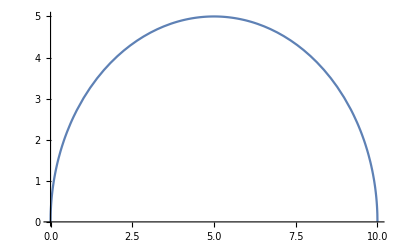

```mathematica
Plot[Sqrt[x]*Sqrt[2*5-x],{x,0,10}]
```

```mathematica
Integrate[Integrate[x*y*sigma,{y,0,Sqrt[x]*Sqrt[2*R-x]},Assumptions->R>0],{x,0,2*R},Assumptions->R>0]
```

(2 R^4 sigma)/3

```mathematica
It={{(1/2)*Pi*R^4*sigma,-2*R^4*sigma/3,0},{-2*R^4*sigma/3,5*Pi*R^4*sigma/8,0},{0,0,6*Pi*R^4*sigma/8}}
```

{{1/2 π R^4 sigma,-(2 R^4 sigma)/3,0},{-(2 R^4 sigma)/3,5/8 π R^4 sigma,0},{0,0,3/4 π R^4 sigma}}

```mathematica
It=It//MatrixForm
```

(1/2 π R^4 sigma | -(2 R^4 sigma)/3 | 0
-(2 R^4 sigma)/3 | 5/8 π R^4 sigma | 0
0 | 0 | 3/4 π R^4 sigma)

```mathematica
wt={{w/Sqrt[2]},{w/Sqrt[2]},{0}}
```

{{w/(√2)},{w/(√2)},{0}}

```mathematica
wt=wt//MatrixForm
```

(w/(√2)
w/(√2)
0)

```mathematica
It.wt
```

{{-1/3 √2 R^4 sigma w+(π R^4 sigma w)/(2 √2)},{-1/3 √2 R^4 sigma w+(5 π R^4 sigma w)/(8 √2)},{0}}